```mathematica
tf=Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth_balance.tfi","XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

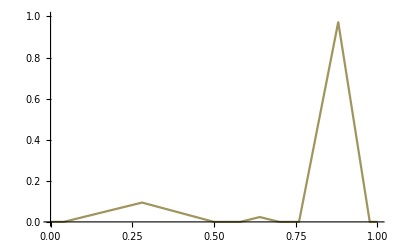

```mathematica
intensity0=intensity;
alpha0=alpha;
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0]];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]
```

```mathematica
d = Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth.tif","Image3D"];
dtf=Image3D[d,ColorFunction->rgbafunction]
```

```mathematica
pos=intensity[[#]]&/@Position[alpha,_?(#==0&)];
features=Table[ImageApply[If[#≥First[pos[[i]]] && #≤First[pos[[i+1]]],1,0]&,d],{i,1,Length[pos],2}]
chartcolors=rgbcolors[[#]]&/@Position[alpha,_?(#>0&)]//Flatten//Lighter;
```

```mathematica
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d5a=Image3D[list3];
d5=ImageRotate[d5a,{90 Degree,{1,0,0}}]
```

```mathematica
list4=Table[ImageApply[List@@rgbfunction[#]&,{list[[i]]}],{i,1,count}];
list5=Table[ImageApply[f[#]&,{list[[i]]}],{i,1,count}];
```

```mathematica
opacity=ImageApply[f[#]&,d];
diff=ImageSubtract[opacity,d5]//ImageAdjust;
r=ImageApply[{1,1,1,#2}*List@@rgbafunction[#1]&,{d,diff}]//Image3D[#,ColorSpace->"RGB"]&
dog1=ImageSubtract[GaussianFilter[opacity,2],GaussianFilter[opacity,4]];
dog2=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]
```

```mathematica
bin=MorphologicalComponents[d]//Colorize[#]&;
distance=DistanceTransform[bin]//ImageAdjust;
zero=ImageResize[Image3D[ConstantArray[0,{1,1,1}]],ImageDimensions[d]];
com=ColorCombine[{ImageAdjust[d],distance,zero}];
cl=ClusteringComponents[com,4];
```

```mathematica
(*ClusteringComponents[com,3]//Colorize[#-1]&*)
(*shell=ClusteringComponents[com,4]//Colorize[(#-1)/.{2->0,3->0}]&;
MorphologicalComponents[shell]//Colorize[#]&*)
(*ClusteringComponents[d,3]//Colorize[#-1]&
ClusteringComponents[d,4]//Colorize[#-1]&*)
(*Transpose[{Flatten@ImageData[d],Flatten@ImageData[distance]}]//ListPlot[#,PlotRange->{{0,1},{0,1}}]&*)
```

```mathematica
feature1=Clip[(cl/.{1->0,2->0,3->0})-1,{0,1}]//Image3D;
feature2=Clip[(cl/.{1->0,2->0,4->0})-1,{0,1}]//Image3D;
feature3=Clip[(cl/.{1->0,3->0,4->0})-1,{0,1}]//Image3D;
```

{0.311085,0.232519,0.456396}

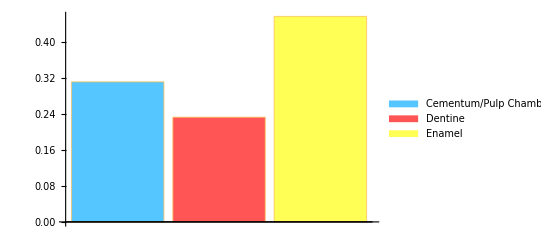

```mathematica
visibility=Table[ImageApply[#*#2&,{d5,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[d5,"TotalIntensity"]&,{i,Length[features]}]
BarChart[visibility,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
```

{0.0336037,0.0814317,0.0380594}

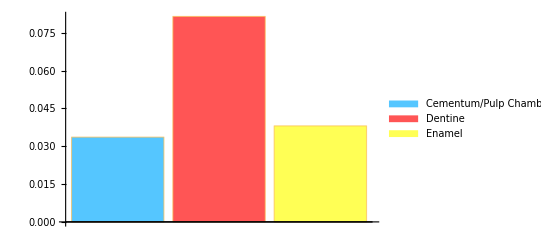

```mathematica
dog=ImageAdjust[dog2];
saliency=Table[ImageApply[#*#2&,{dog,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"]&,{i,Length[features]}]
BarChart[saliency,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
```

{0.257939,0.183563,0.558498}

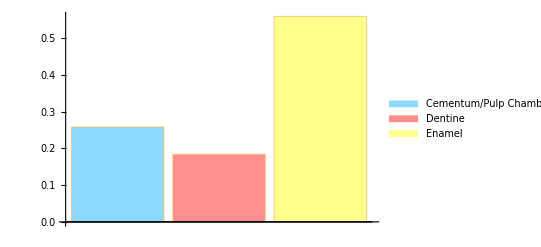

```mathematica
ss=ImageApply[#*#2&,{dog,d5}];
vs=Table[ImageApply[#*#2*#3&,{dog,features[[i]],d5}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[ss,"TotalIntensity"]&,{i,Length[features]}]
BarChart[vs,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->(chartcolors//Lighter)]
```

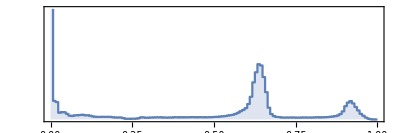

```mathematica
ImageHistogram[d]
```

```mathematica
Export[NotebookDirectory[]<>"Tooth_RGBA_2.raw",Flatten@ImageData[r,"Byte"],{"Binary","Byte"}];
Export[NotebookDirectory[]<>"Tooth_visibility_2.raw",Flatten@ImageData[d5,"Byte"],{"Binary","Byte"}];
```